## Product of two normal random variables

## Checking the distribution functions

### Generating two normal random variables

```mathematica
n0= 100000; (* numnber of samples *)
```

```mathematica
data1=RandomVariate[NormalDistribution[0,1],n0];
```

```mathematica
data2=RandomVariate[NormalDistribution[0,1],n0];
```

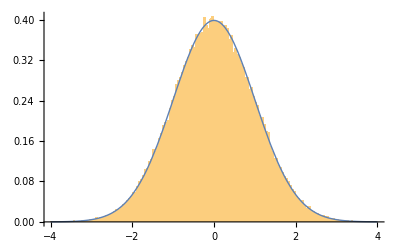

```mathematica
Show[Histogram[data1,{-4,4,0.05},"ProbabilityDensity"],Plot[PDF[NormalDistribution[0,1],x],{x,-4,4},PlotStyle->Thick,PlotRange->All]]
```

### Generating the product of two normal random variables

```mathematica
data3 = data1 * data2;
```

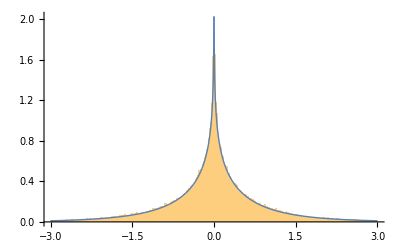

```mathematica
Show[Histogram[data3,{-3,3,0.02},"ProbabilityDensity"],Plot[BesselK[0,Abs[x]]/π,{x,-3,3},PlotStyle->Thick,PlotRange->All]]
```

## P-values for normal and the product of two normals

### Numerical evaluations

```mathematica
precision0 = 500; (* precision for computing p-values *)
```

```mathematica
SetPrecision0[x_]:=SetPrecision[x,precision0]
```

```mathematica
precision1 = 20; (* precision for outputs *)
```

```mathematica
N1[x_]:=N[x,precision1]
```

### Tail probability of normal random variable

```mathematica
tailnormal[x_]=Integrate[PDF[NormalDistribution[0,1],t],{t,Abs[x],∞}]
```

1/2 Erfc[Abs[x]/(√2)]

```mathematica
tailnormal[SetPrecision0[10.0]]
```

7.61985302416052606597334325159930836350403327795696057803535546289661562205964817033415138518280467160816303822798982989719817061433818260352289351220224590607303114569218382246575889987628945983087201467435763059338028661837282329049977866133468168608845111387450081580779476695749879309370512448222155381480643821614260864519547729676283754087020348196053200926263034792474111117309810626001221936551334469548912147659706213685301067966246882993494705325862973629272337123×10^-24

```mathematica
N1[tailnormal[SetPrecision0[10.0]]]
```

7.619853024160526066×10^-24

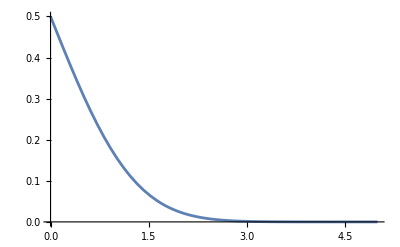

```mathematica
Plot[tailnormal[x],{x,0,5}]
```

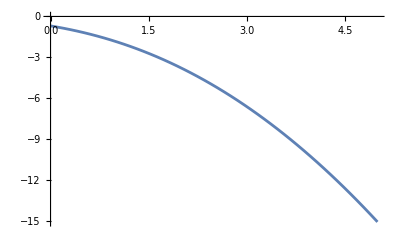

```mathematica
Plot[Log[tailnormal[x]],{x,0,5}]
```

### Tail probability of the product of two normal random variables

```mathematica
tailbessel[x_]=1/2-Integrate[BesselK[0,t],{t,0,Abs[x]}]/π
```

1/2-1/2 Abs[x] (BesselK[0,Abs[x]] StruveL[-1,Abs[x]]+BesselK[1,Abs[x]] StruveL[0,Abs[x]])

```mathematica
tailbessel[SetPrecision0[100.0]]
```

1.474965847260806879759028614382444053887587255979803382535937983652503630444340329652346181545583067481632113334787415282099548936259248128201919609647878099155083372504484001008253400072230753167194501557109016543584846494046148522518389102791496240357489999869628390973958445448217305520271575516822633367044265337374724679325340144657206440939267080767327864725484980355666783377197352521776264303907857830843386225045861154264165114910057465617437706×10^-45

```mathematica
N1[tailbessel[SetPrecision0[100.0]]]
```

1.4749658472608068798×10^-45

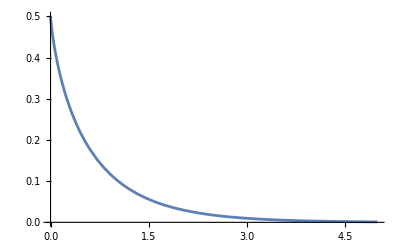

```mathematica
Plot[tailbessel[x],{x,0,5},PlotRange->All]
```

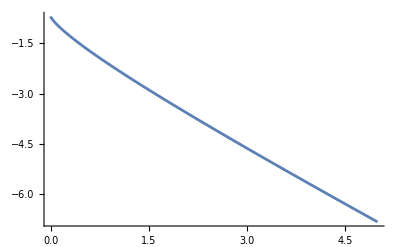

```mathematica
Plot[Log[tailbessel[x]],{x,0,5},PlotRange->All]
```

### P-values for embeddings

one-sided p-value for the elements of embeddings with dimensions d

```mathematica
PvalueNormal[x_,d_]:=tailnormal[x Sqrt[d]]
```

one-sided p-value for the products of two elements of embeddings with dimensions d

```mathematica
PvalueProduct[x_,d_]:=tailbessel[x d]
```

### Compare

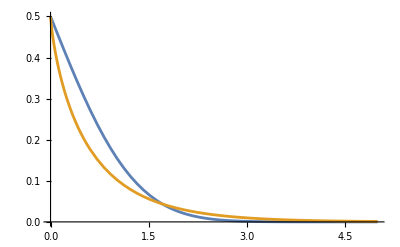

```mathematica
Plot[{tailnormal[x],tailbessel[x]},{x,0,5},PlotRange->All]
```

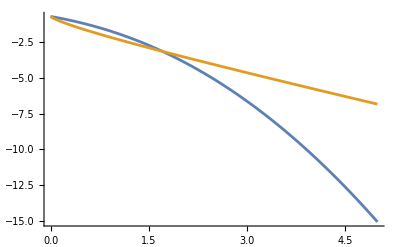

```mathematica
Plot[{Log[tailnormal[x]],Log[tailbessel[x]]},{x,0,5},PlotRange->All]
```

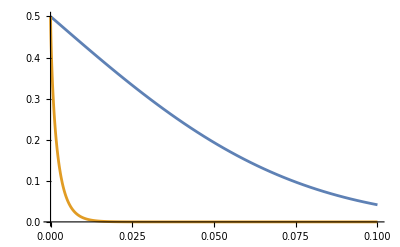

```mathematica
Plot[{PvalueNormal[x,300],PvalueProduct[x,300]},{x,0,0.1},PlotRange->All]
```

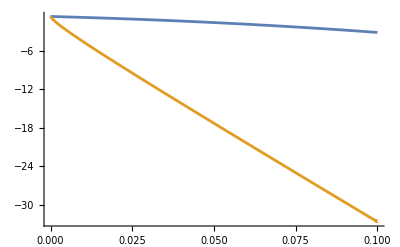

```mathematica
Plot[{Log[PvalueNormal[x,300]],Log[PvalueProduct[x,300]]},{x,0,0.1},PlotRange->All]
```

## GloVe ICA

### setting

```mathematica
filename = "data/glove_ica"; (* base name for input csv *)
```

```mathematica
pvnum = 10; (* number of p-values shown in this notebook *)
```

### loading embeddings

```mathematica
embeddings = Import[FileNameJoin[{NotebookDirectory[],filename <>".csv"}]];
```

```mathematica
Dimensions[embeddings]
```

{2,301}

```mathematica
d0 = Dimensions[embeddings][[2]]-1 (* dimensions *)
```

300

```mathematica
embeddings[[1;;2,1]]
```

{ultraviolet,light}

```mathematica
embedding1 = Table[embeddings[[1]][[i+1]],{i,1,d0}];
```

```mathematica
embedding2 = Table[embeddings[[2]][[i+1]],{i,1,d0}];
```

```mathematica
product = embedding1 embedding2;
```

### largest elements

```mathematica
Reverse[Sort[Abs[embedding1]]][[1;;pvnum]]
```

{0.534778,0.26525,0.219918,0.142215,0.140345,0.135273,0.123291,0.118807,0.112031,0.10384}

```mathematica
Reverse[Sort[Abs[embedding2]]][[1;;pvnum]]
```

{0.553637,0.3788,0.23018,0.114424,0.113606,0.110458,0.108315,0.105231,0.103104,0.102278}

```mathematica
Reverse[Sort[Abs[product]]][[1;;pvnum]]
```

{0.296073,0.030351,0.0224457,0.0140396,0.00698963,0.00558748,0.0053346,0.00516984,0.00512847,0.00509834}

### computing p-values

```mathematica
pvalue1 = Table[PvalueNormal[SetPrecision0[embedding1[[i]]],d0],{i,1,d0}];
```

```mathematica
pvalue2 = Table[PvalueNormal[SetPrecision0[embedding2[[i]]],d0],{i,1,d0}];
```

```mathematica
pvalue3 = Table[PvalueProduct[SetPrecision0[product[[i]]],d0],{i,1,d0}];
```

### truncate digits

```mathematica
pvalue1 = N1[pvalue1];
```

```mathematica
pvalue2 = N1[pvalue2];
```

```mathematica
pvalue3= N1[pvalue3];
```

### smallest p - values

```mathematica
Sort[pvalue1][[1;;pvnum]]
```

{9.9727102109255499839×10^-21,2.1713253147956397236×10^-6,0.000069741544648986716679,0.0068846028396609071991,0.0075316452423573268084,0.0095645911121902092716,0.016361578793168615862,0.019804368158821912148,0.026163923335786963767,0.036043532415242638207}

```mathematica
Sort[pvalue2][[1;;pvnum]]
```

{4.4352624838040532268×10^-22,2.6721118617412933276×10^-11,0.000033480324678891397434,0.023746355809461928765,0.024550463178974927537,0.0278623577395691013,0.030323093636972657604,0.034177578312293119273,0.037064199102258047676,0.038238320398020305428}

```mathematica
Sort[pvalue3][[1;;pvnum]]
```

{1.1188250686729021116×10^-40,0.00001381883516521066403,0.0001690006643712184715,0.0025596168912095961888,0.027602292082712734552,0.045359478539450394649,0.049683428069175252811,0.052734854137595203625,0.053532084761371115616,0.054120792586203003736}

### histogram of p - values

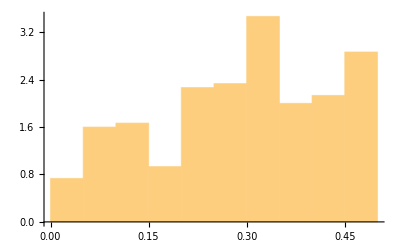

```mathematica
Show[Histogram[pvalue1,10,"ProbabilityDensity"],PlotStyle->Thick,PlotRange->All]
```

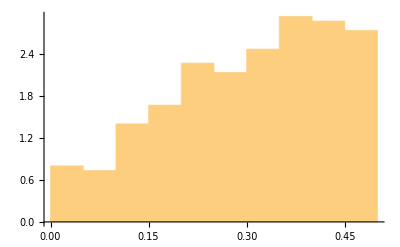

```mathematica
Show[Histogram[pvalue2,10,"ProbabilityDensity"],PlotStyle->Thick,PlotRange->All]
```

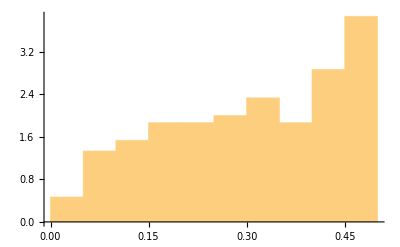

```mathematica
Show[Histogram[pvalue3,10,"ProbabilityDensity"],PlotStyle->Thick,PlotRange->All]
```

### output p - values

```mathematica
pvalues = {pvalue1,pvalue2,pvalue3};
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],filename <>"-pvalue.csv"}],pvalues,"CSV"];
```

## GloVe PCA

### setting

```mathematica
filename = "data/glove_pca"; (* base name for input csv *)
```

```mathematica
pvnum = 10; (* number of p-values shown in this notebook *)
```

### loading embeddings

```mathematica
embeddings = Import[FileNameJoin[{NotebookDirectory[],filename <>".csv"}]];
```

```mathematica
Dimensions[embeddings]
```

{2,301}

```mathematica
d0 = Dimensions[embeddings][[2]]-1 (* dimensions *)
```

300

```mathematica
embeddings[[1;;2,1]]
```

{ultraviolet,light}

```mathematica
embedding1 = Table[embeddings[[1]][[i+1]],{i,1,d0}];
```

```mathematica
embedding2 = Table[embeddings[[2]][[i+1]],{i,1,d0}];
```

```mathematica
product = embedding1 embedding2;
```

### largest elements

```mathematica
Reverse[Sort[Abs[embedding1]]][[1;;pvnum]]
```

{0.202355,0.197082,0.174948,0.172482,0.157429,0.152461,0.150836,0.150187,0.145999,0.137225}

```mathematica
Reverse[Sort[Abs[embedding2]]][[1;;pvnum]]
```

{0.247417,0.215653,0.176051,0.175901,0.174256,0.158521,0.145853,0.139102,0.132596,0.132584}

```mathematica
Reverse[Sort[Abs[product]]][[1;;pvnum]]
```

{0.0238298,0.0216126,0.0199125,0.0193315,0.0170272,0.016883,0.0165086,0.0164595,0.0160765,0.0149764}

### computing p-values

```mathematica
pvalue1 = Table[PvalueNormal[SetPrecision0[embedding1[[i]]],d0],{i,1,d0}];
```

```mathematica
pvalue2 = Table[PvalueNormal[SetPrecision0[embedding2[[i]]],d0],{i,1,d0}];
```

```mathematica
pvalue3 = Table[PvalueProduct[SetPrecision0[product[[i]]],d0],{i,1,d0}];
```

### truncate digits

```mathematica
pvalue1 = N1[pvalue1];
```

```mathematica
pvalue2 = N1[pvalue2];
```

```mathematica
pvalue3= N1[pvalue3];
```

### smallest p - values

```mathematica
Sort[pvalue1][[1;;pvnum]]
```

{0.00022839928633589803818,0.00032060091970176385135,0.001222029829810036531,0.0014064722338352894975,0.0031980699317959966585,0.0041367850647829578809,0.0044933789779931705359,0.0046432738151138379601,0.0057231311587856054694,0.008731490431435110295}

```mathematica
Sort[pvalue2][[1;;pvnum]]
```

{9.1211573884210215832×10^-6,0.00009377599542006898265,0.0011469165033407148393,0.0011568427843692526073,0.0012714064817999535993,0.0030193601548346359915,0.0057645362598260298737,0.007991241858854561008,0.010820121694564395228,0.010825748986848787497}

```mathematica
Sort[pvalue3][[1;;pvnum]]
```

{0.00010872410728436849796,0.00022054231403184558623,0.00038034992569077376276,0.000458488950530475183,0.00096525251477809166805,0.0010114822384612679314,0.0011422849040823331301,0.0011606722152273658583,0.0013146980990276005761,0.0018825981529722625625}

### histogram of p - values

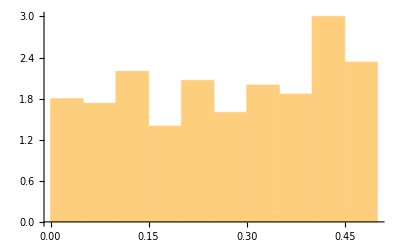

```mathematica
Show[Histogram[pvalue1,10,"ProbabilityDensity"],PlotStyle->Thick,PlotRange->All]
```

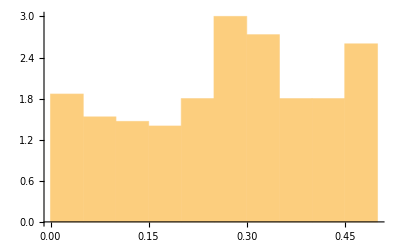

```mathematica
Show[Histogram[pvalue2,10,"ProbabilityDensity"],PlotStyle->Thick,PlotRange->All]
```

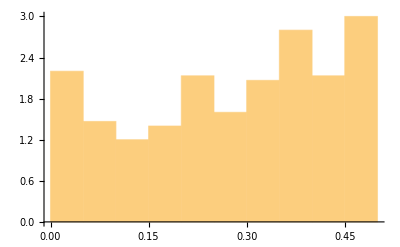

```mathematica
Show[Histogram[pvalue3,10,"ProbabilityDensity"],PlotStyle->Thick,PlotRange->All]
```

### output p - values

```mathematica
pvalues = {pvalue1,pvalue2,pvalue3};
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],filename <>"-pvalue.csv"}],pvalues,"CSV"];
```

## Pythia ICA

### setting

```mathematica
filename = "data/EleutherAI-pythia-160m_ica"; (* base name for input csv *)
```

```mathematica
pvnum = 10; (* number of p-values shown in this notebook *)
```

### loading embeddings

```mathematica
embeddings = Import[FileNameJoin[{NotebookDirectory[],filename <>".csv"}]];
```

```mathematica
Dimensions[embeddings]
```

{2,769}

```mathematica
d0 = Dimensions[embeddings][[2]]-1 (* dimensions *)
```

768

```mathematica
embeddings[[1;;2,1]]
```

{ultraviolet,light}

```mathematica
embedding1 = Table[embeddings[[1]][[i+1]],{i,1,d0}];
```

```mathematica
embedding2 = Table[embeddings[[2]][[i+1]],{i,1,d0}];
```

```mathematica
product = embedding1 embedding2;
```

### largest elements

```mathematica
Reverse[Sort[Abs[embedding1]]][[1;;pvnum]]
```

{0.601093,0.149198,0.115575,0.107548,0.0933143,0.0887963,0.0874292,0.0872673,0.0863517,0.0861818}

```mathematica
Reverse[Sort[Abs[embedding2]]][[1;;pvnum]]
```

{0.645316,0.150569,0.122209,0.116203,0.11412,0.0897541,0.087483,0.0742343,0.0738345,0.0729211}

```mathematica
Reverse[Sort[Abs[product]]][[1;;pvnum]]
```

{0.387895,0.0224646,0.0101595,0.00820432,0.00636319,0.00564241,0.00505327,0.00499439,0.00494187,0.00470642}

### computing p-values

```mathematica
pvalue1 = Table[PvalueNormal[SetPrecision0[embedding1[[i]]],d0],{i,1,d0}];
```

```mathematica
pvalue2 = Table[PvalueNormal[SetPrecision0[embedding2[[i]]],d0],{i,1,d0}];
```

```mathematica
pvalue3 = Table[PvalueProduct[SetPrecision0[product[[i]]],d0],{i,1,d0}];
```

### truncate digits

```mathematica
pvalue1 = N1[pvalue1];
```

```mathematica
pvalue2 = N1[pvalue2];
```

```mathematica
pvalue3= N1[pvalue3];
```

### smallest p - values

```mathematica
Sort[pvalue1][[1;;pvnum]]
```

{1.3239142906559974835×10^-62,0.000017771101896645251444,0.00068024897130484095416,0.0014390529714906372219,0.0048548028188086393439,0.006931495958530492361,0.0076984070204372019074,0.0077940149304908772344,0.0083544973808554944126,0.0084623453416663916636}

```mathematica
Sort[pvalue2][[1;;pvnum]]
```

{7.9232621737520507911×10^-72,0.000015051031511772283297,0.0003536058649579579031,0.00064027447504858993164,0.00078185208595102264153,0.0064351209499248656046,0.0076668636102040126032,0.019831526361069609108,0.020370185096259333318,0.021647709013704370874}

```mathematica
Sort[pvalue3][[1;;pvnum]]
```

{9.6611899412734605431×10^-132,2.9852622069772292607×10^-9,0.000054438766188290305294,0.0002680600532322806074,0.0012265298513882333376,0.0022408909464902746386,0.0036823577461693833587,0.0038706362305930553459,0.0040468768615758205433,0.0049431317624192937295}

### histogram of p - values

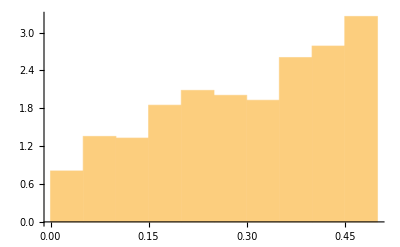

```mathematica
Show[Histogram[pvalue1,10,"ProbabilityDensity"],PlotStyle->Thick,PlotRange->All]
```

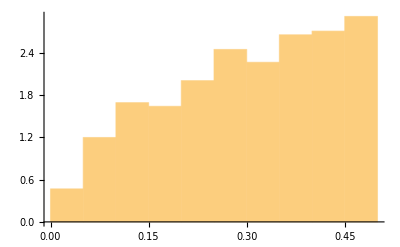

```mathematica
Show[Histogram[pvalue2,10,"ProbabilityDensity"],PlotStyle->Thick,PlotRange->All]
```

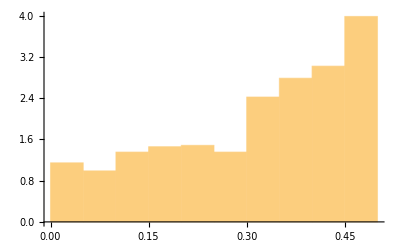

```mathematica
Show[Histogram[pvalue3,10,"ProbabilityDensity"],PlotStyle->Thick,PlotRange->All]
```

### output p - values

```mathematica
pvalues = {pvalue1,pvalue2,pvalue3};
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],filename <>"-pvalue.csv"}],pvalues,"CSV"];
```

## Pythia PCA

### setting

```mathematica
filename = "data/EleutherAI-pythia-160m_pca"; (* base name for input csv *)
```

```mathematica
pvnum = 10; (* number of p-values shown in this notebook *)
```

### loading embeddings

```mathematica
embeddings = Import[FileNameJoin[{NotebookDirectory[],filename <>".csv"}]];
```

```mathematica
Dimensions[embeddings]
```

{2,769}

```mathematica
d0 = Dimensions[embeddings][[2]]-1 (* dimensions *)
```

768

```mathematica
embeddings[[1;;2,1]]
```

{ultraviolet,light}

```mathematica
embedding1 = Table[embeddings[[1]][[i+1]],{i,1,d0}];
```

```mathematica
embedding2 = Table[embeddings[[2]][[i+1]],{i,1,d0}];
```

```mathematica
product = embedding1 embedding2;
```

### largest elements

```mathematica
Reverse[Sort[Abs[embedding1]]][[1;;pvnum]]
```

{0.125502,0.121365,0.0973242,0.0957124,0.0929038,0.0920286,0.0914271,0.0909184,0.0898081,0.0876936}

```mathematica
Reverse[Sort[Abs[embedding2]]][[1;;pvnum]]
```

{0.128636,0.113207,0.10435,0.103102,0.101709,0.101052,0.0995926,0.0989615,0.0986276,0.0978361}

```mathematica
Reverse[Sort[Abs[product]]][[1;;pvnum]]
```

{0.0156119,0.0129396,0.00768797,0.00764188,0.00667392,0.00666742,0.00645442,0.006219,0.0061793,0.00616578}

### computing p-values

```mathematica
pvalue1 = Table[PvalueNormal[SetPrecision0[embedding1[[i]]],d0],{i,1,d0}];
```

```mathematica
pvalue2 = Table[PvalueNormal[SetPrecision0[embedding2[[i]]],d0],{i,1,d0}];
```

```mathematica
pvalue3 = Table[PvalueProduct[SetPrecision0[product[[i]]],d0],{i,1,d0}];
```

### truncate digits

```mathematica
pvalue1 = N1[pvalue1];
```

```mathematica
pvalue2 = N1[pvalue2];
```

```mathematica
pvalue3= N1[pvalue3];
```

### smallest p - values

```mathematica
Sort[pvalue1][[1;;pvnum]]
```

{0.00025256038822062073907,0.00038497381789775003943,0.0034970315579463093691,0.0039953940157082905983,0.0050174489478795269111,0.0053803973158651800971,0.0056432276757008489033,0.0058743490944086947131,0.0064081171035014159542,0.0075445040780099606809}

```mathematica
Sort[pvalue2][[1;;pvnum]]
```

{0.00018202781334466191715,0.00085256834212590114958,0.0019149984644905975316,0.0021366729418871678656,0.0024113984950979447977,0.00255162874251644035,0.0028901409804209738951,0.0030486483008225889579,0.0031356652741908659164,0.0033508684914258616032}

```mathematica
Sort[pvalue3][[1;;pvnum]]
```

{6.8193423690938106586×10^-7,5.7812168629015303849×10^-6,0.00040969992413534862805,0.00042554566707283324162,0.0009472558036194627488,0.00095238527597095750162,0.0011368312340156486596,0.0013831515735792064068,0.0014297337542016547266,0.001445948083241226915}

### histogram of p - values

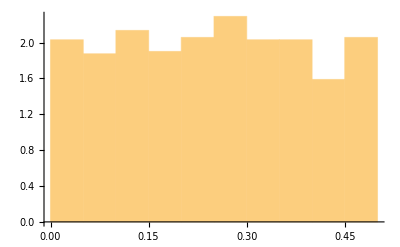

```mathematica
Show[Histogram[pvalue1,10,"ProbabilityDensity"],PlotStyle->Thick,PlotRange->All]
```

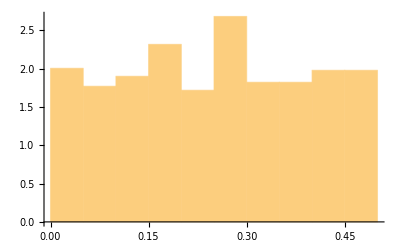

```mathematica
Show[Histogram[pvalue2,10,"ProbabilityDensity"],PlotStyle->Thick,PlotRange->All]
```

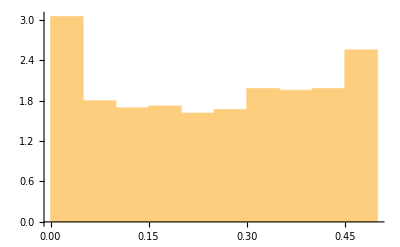

```mathematica
Show[Histogram[pvalue3,10,"ProbabilityDensity"],PlotStyle->Thick,PlotRange->All]
```

### output p - values

```mathematica
pvalues = {pvalue1,pvalue2,pvalue3};
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],filename <>"-pvalue.csv"}],pvalues,"CSV"];
```

## GPT2 ICA

### setting

```mathematica
filename = "data/gpt2_ica"; (* base name for input csv *)
```

```mathematica
pvnum = 10; (* number of p-values shown in this notebook *)
```

### loading embeddings

```mathematica
embeddings = Import[FileNameJoin[{NotebookDirectory[],filename <>".csv"}]];
```

```mathematica
Dimensions[embeddings]
```

{2,769}

```mathematica
d0 = Dimensions[embeddings][[2]]-1 (* dimensions *)
```

768

```mathematica
embeddings[[1;;2,1]]
```

{ultraviolet,light}

```mathematica
embedding1 = Table[embeddings[[1]][[i+1]],{i,1,d0}];
```

```mathematica
embedding2 = Table[embeddings[[2]][[i+1]],{i,1,d0}];
```

```mathematica
product = embedding1 embedding2;
```

### largest elements

```mathematica
Reverse[Sort[Abs[embedding1]]][[1;;pvnum]]
```

{0.412892,0.274985,0.156069,0.123778,0.117139,0.11502,0.102941,0.101257,0.0992244,0.0991805}

```mathematica
Reverse[Sort[Abs[embedding2]]][[1;;pvnum]]
```

{0.449752,0.321907,0.144877,0.128259,0.122076,0.121777,0.110015,0.103546,0.100394,0.0971766}

```mathematica
Reverse[Sort[Abs[product]]][[1;;pvnum]]
```

{0.185699,0.0885194,0.0190056,0.0179326,0.0127208,0.0102743,0.0099823,0.00776384,0.00774396,0.00518704}

### computing p-values

```mathematica
pvalue1 = Table[PvalueNormal[SetPrecision0[embedding1[[i]]],d0],{i,1,d0}];
```

```mathematica
pvalue2 = Table[PvalueNormal[SetPrecision0[embedding2[[i]]],d0],{i,1,d0}];
```

```mathematica
pvalue3 = Table[PvalueProduct[SetPrecision0[product[[i]]],d0],{i,1,d0}];
```

### truncate digits

```mathematica
pvalue1 = N1[pvalue1];
```

```mathematica
pvalue2 = N1[pvalue2];
```

```mathematica
pvalue3= N1[pvalue3];
```

### smallest p - values

```mathematica
Sort[pvalue1][[1;;pvnum]]
```

{1.2834480284074826699×10^-30,1.2625316958177614424×10^-14,7.6225439022690687637×10^-6,0.00030151394852150871834,0.00058468433670341731773,0.00071744930048294055338,0.0021669612570376461191,0.0025070447163681984033,0.0029817028989625085584,0.0029927759619287111553}

```mathematica
Sort[pvalue2][[1;;pvnum]]
```

{5.8756053956656604701×10^-36,2.3117635174655319148×10^-19,0.000029730617483487919122,0.00018941500365791267579,0.00035839769444402885142,0.00036937558852008958569,0.0011486739457767337609,0.002055222015285777384,0.0026996042333217114831,0.0035402288811217061808}

```mathematica
Sort[pvalue3][[1;;pvnum]]
```

{3.8397613293868146788×10^-64,1.4328633660188202127×10^-31,4.5974783925943615532×10^-8,1.0766629659811503079×10^-7,6.8915619827463771374×10^-6,0.00004959903817369698104,0.000062857747404859980855,0.00038490385259725407147,0.00039125151305702764793,0.0032884394819215879927}

### histogram of p - values

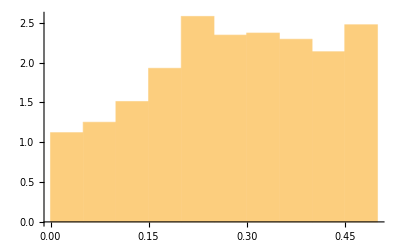

```mathematica
Show[Histogram[pvalue1,10,"ProbabilityDensity"],PlotStyle->Thick,PlotRange->All]
```

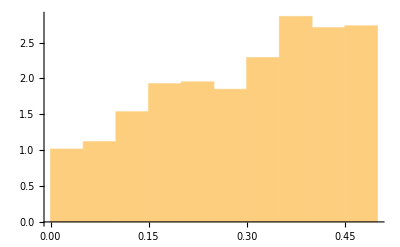

```mathematica
Show[Histogram[pvalue2,10,"ProbabilityDensity"],PlotStyle->Thick,PlotRange->All]
```

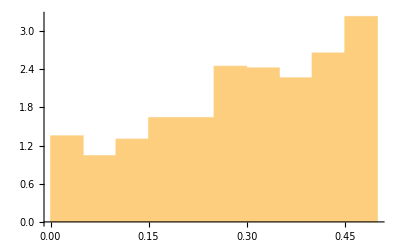

```mathematica
Show[Histogram[pvalue3,10,"ProbabilityDensity"],PlotStyle->Thick,PlotRange->All]
```

### output p - values

```mathematica
pvalues = {pvalue1,pvalue2,pvalue3};
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],filename <>"-pvalue.csv"}],pvalues,"CSV"];
```

## GPT2 PCA

### setting

```mathematica
filename = "data/gpt2_pca"; (* base name for input csv *)
```

```mathematica
pvnum = 10; (* number of p-values shown in this notebook *)
```

### loading embeddings

```mathematica
embeddings = Import[FileNameJoin[{NotebookDirectory[],filename <>".csv"}]];
```

```mathematica
Dimensions[embeddings]
```

{2,769}

```mathematica
d0 = Dimensions[embeddings][[2]]-1 (* dimensions *)
```

768

```mathematica
embeddings[[1;;2,1]]
```

{ultraviolet,light}

```mathematica
embedding1 = Table[embeddings[[1]][[i+1]],{i,1,d0}];
```

```mathematica
embedding2 = Table[embeddings[[2]][[i+1]],{i,1,d0}];
```

```mathematica
product = embedding1 embedding2;
```

### largest elements

```mathematica
Reverse[Sort[Abs[embedding1]]][[1;;pvnum]]
```

{0.108743,0.101386,0.0995225,0.095572,0.0955223,0.0949627,0.0922943,0.0883422,0.086621,0.083538}

```mathematica
Reverse[Sort[Abs[embedding2]]][[1;;pvnum]]
```

{0.127528,0.114267,0.101612,0.101204,0.100394,0.0979855,0.0977297,0.0936943,0.090686,0.0897086}

```mathematica
Reverse[Sort[Abs[product]]][[1;;pvnum]]
```

{0.0095899,0.00946041,0.00935614,0.00921621,0.00715787,0.00666351,0.00657745,0.00601056,0.00589385,0.00566825}

### computing p-values

```mathematica
pvalue1 = Table[PvalueNormal[SetPrecision0[embedding1[[i]]],d0],{i,1,d0}];
```

```mathematica
pvalue2 = Table[PvalueNormal[SetPrecision0[embedding2[[i]]],d0],{i,1,d0}];
```

```mathematica
pvalue3 = Table[PvalueProduct[SetPrecision0[product[[i]]],d0],{i,1,d0}];
```

### truncate digits

```mathematica
pvalue1 = N1[pvalue1];
```

```mathematica
pvalue2 = N1[pvalue2];
```

```mathematica
pvalue3= N1[pvalue3];
```

### smallest p - values

```mathematica
Sort[pvalue1][[1;;pvnum]]
```

{0.0012909648877135171132,0.0024794282531022847861,0.0029073704813826130227,0.0040416670610177599312,0.0040581838063236048641,0.0042481446866775299171,0.0052678388480166798726,0.0071783988190064237491,0.0081860786565549845988,0.010304490946062993381}

```mathematica
Sort[pvalue2][[1;;pvnum]]
```

{0.00020453589951324273447,0.00077103772939661159025,0.0024315389463037215391,0.0025185733333578072587,0.0026994821066789520628,0.0033092381255084655907,0.0033807768748035388519,0.00470850446531035633,0.0059826855260951623546,0.00645798494173343725}

```mathematica
Sort[pvalue3][[1;;pvnum]]
```

{0.000086465316887109256062,0.000096073535574114030709,0.00010458580245612786567,0.00011721540928606733259,0.00063439377173455608527,0.00095548025250574422175,0.0010262859085048966571,0.0016461183196612757607,0.0018149479371583577933,0.0021927956490081359983}

### histogram of p - values

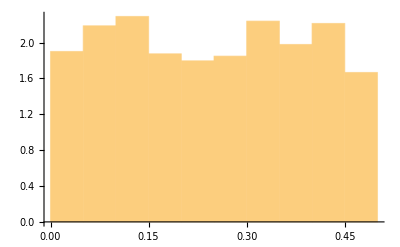

```mathematica
Show[Histogram[pvalue1,10,"ProbabilityDensity"],PlotStyle->Thick,PlotRange->All]
```

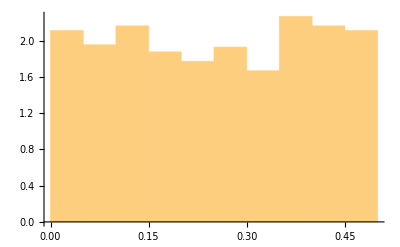

```mathematica
Show[Histogram[pvalue2,10,"ProbabilityDensity"],PlotStyle->Thick,PlotRange->All]
```

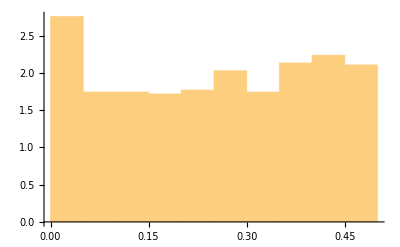

```mathematica
Show[Histogram[pvalue3,10,"ProbabilityDensity"],PlotStyle->Thick,PlotRange->All]
```

### output p - values

```mathematica
pvalues = {pvalue1,pvalue2,pvalue3};
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],filename <>"-pvalue.csv"}],pvalues,"CSV"];
```